# Theorems

There are lots of theorems in Chapter 4.  They are useful in at least three different ways!
1) They sometimes let us compute things efficiently.
2) They promise that things exist and usually that there is only one such thing.
3) They give different representations of the same thing.  Sometimes one representation makes a useful property obvious. 
Anyway we are going to check some of the properties promised by the theorems in Chapter 4.

## Theorems

### Theorem 4.1 p95 (Fundamental Theorem)

If F'(z)=f(z) then ∫_z_a^z_b f(z)dz=F(z_b)-F(z_a).

### Theorem 4.2 p96 (Cauchy)

∮_Γ f(z)dz=0 when f is analytic and singularity free inside the closed contour Γ.

### Theorem 4.3 p97 (Morera)

If ∮_Γ f(z)dz=0 for every closed contour Γ inside a domain 𝒟 then f is analytic on 𝒟.

### Theorem 4.6 p100 (Pole Computation)

1/(2π ⅈ)∮_Γ 1/(z-z_0)^n dz=Piecewise[{{1, if n=1 and z_0 is inside Γ}, {0, if n≠1or z_0 is outside Γ}}]

### Theorem 4.8 p101 (Cauchy Argument P)

If f is meromorphic with n zeros and p poles inside a closed CCW contour Γ then
	n-p= 1/(2π ⅈ)∮_Γ (f'(z))/(f(z))dz

### Theorem 4.10 p102 (Cauchy Integral F)

If f is analytic inside a closed CCW contour Γ then
	f(z)=1/(2π ⅈ)∮_Γ (f(ζ))/(ζ-z)dζ
and a similar formula holds for any derivative
	f^(k)(z)=(k!)/(2π ⅈ)∮_Γ (f(ζ))/(ζ-z)^(k+1)dζ.

### Theorem 4.12 p103 (Liouville)

If f is entire and bounded |f(z)|≤ M then f is a constant function.

Proof hint: estimate a_k in a Taylor Series about z_0 using Cauchy Int F. 
	|a_k|=|1/(2π ⅈ)∮ _(C_r(z_0)) (f(ζ))/(ζ-z_0)^(k+1)dζ|≤1/(2π)∫_0^(2π)|(f(z_0+r ⅇ^(ⅈ θ)))/((r ⅇ^(ⅈ θ))^(k+1))ⅈ r ⅇ^(ⅈ θ)|dθ.
so 
	|a_k|≤M r/r^(k+1)=M/r^k
Letting r→∞ shows a_k=0 for k=1,2,3,… 
In other words,  f(z)=f(z_0) for all z.
https://en.wikipedia.org/wiki/Liouville%27s_theorem_(complex_analysis)

### Theorem 4.14 and 4.15 p103 (Fundamental Theorem of Algebra)

4.14	A polynomial p(z) has at least one zero.
4.15	A polynomial p(z) of degree n has n zeros.

4.14 proof hint: consider  Liouville theorem for 1/p(z) if p(z) no zeros
4.15 proof hint: induction

### Theorem 4.16 p104 (Mean Value)

For analytic f we have f(z)=1/(2π)∫_0^(2π) f(z+R ⅇ^(ⅈ θ))dθ=1/(2π)∫_0^(2π) u(z+R ⅇ^(ⅈ θ)) + ⅈ v(z+R ⅇ^(ⅈ θ))d

Proof hint: Cauchy Int F on a particular contour.

### Theorem 4.17 and 4.18 p104 (Maximum Principle)

The real and imaginary parts of an analytic function f=u+ⅈ v can not have local maximums or minimums.

Proof hint: For any R u(z)=1/(2π)∫_0^(2π) u(z+R ⅇ^(ⅈ θ))dθ

### Taylor and Series p105-108

TS(z)=∑_(k=-∞)^∞ (a_k(z-z_0))^k on disk 𝒟={z:|z-z_0|< R}
where f is analytic on 𝒟 and c is any simple CCW contour inside 𝒟 
	a_k=(f^(k)(z_0))/(k!)=1/(2π ⅈ)∫_c (f(ζ))/(ζ-z_0)^(k+1)dζ.

LS(z)=∑_(k=-∞)^∞ (a_k(z-z_0))^k on annulus 𝒜={z:R_1< |z-z_0|< R_2}
where f is analytic on 𝒜 and c is any simple CCW contour inside 𝒜 
	a_k=1/(2π ⅈ)∫_c (f(ζ))/(ζ-z_0)^(k+1)dζ.

Note this says that there is exactly one TS/LS about a point z_0.  In other words, these series are uniquely defined.

## Action

### Counting polynomial roots in a region

Suppose I want to count the roots of a polynomial in a region.

#### Code

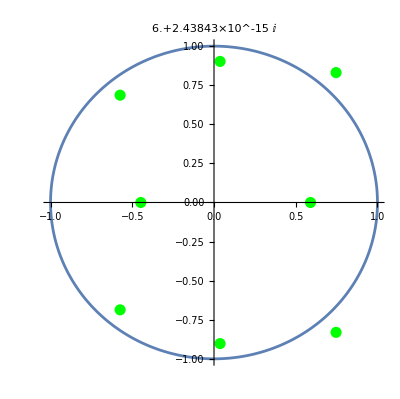

```mathematica
n=10;
f[z_]=z^n+Sum[ RandomInteger[{-9,9}] z^k,{k,0,n-1}];
R=1.0;
p[t_]:= R E^(2π ⅈ t)
roots=NSolveValues[f[z]==0,z];
ParametricPlot[ReIm[p[t]],{t,0,1},
Epilog->{Green, PointSize[0.02],Point[ReIm[roots]]},
PlotLabel->(1/(2π ⅈ))NIntegrate[(f'[p[t]]/f[p[t]])p'[t],{t,0,1}]]
```

It works for any parameterization.

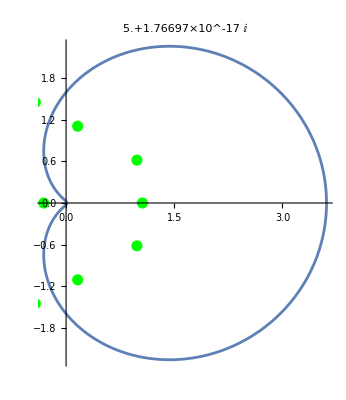

```mathematica
n=12;
f[z_]=z^n+Sum[ RandomInteger[{-9,9}] z^k,{k,0,n-1}];
R=1.4;
p[t_]:= (1+0.9 E^(2π ⅈ t))^2
roots=NSolveValues[f[z]==0,z];
ParametricPlot[ReIm[p[t]],{t,0,1},
Epilog->{Green, PointSize[0.02],Point[ReIm[roots]]},
PlotLabel->(1/(2π ⅈ))NIntegrate[(f'[p[t]]/f[p[t]])p'[t],{t,0,1}]]
```

Even parameterizations that look funky!

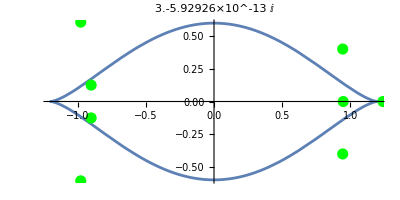

```mathematica
n=18;
f[z_]=z^n+Sum[ RandomInteger[{-9,9}] z^k,{k,0,n-1}];
R=1.2;
p[t_]:= R (Cos[2π t]+ ⅈ 0.5 Sin[2π t]^3)
roots=NSolveValues[f[z]==0,z];
ParametricPlot[ReIm[p[t]],{t,0,1},
Epilog->{Green, PointSize[0.02],Point[ReIm[roots]]},
PlotLabel->(1/(2π ⅈ))NIntegrate[(f'[p[t]]/f[p[t]])p'[t],{t,0,1}]]
```

### Counting function zeros in a region

Count the zeros of a function in a region works the same way.

#### Code

```mathematica
f[z_]=Sin[Cos[z^3]]- I z^2 Cos[z];
R=1.2;
p[t_]:= R E^(2π ⅈ t)
TabView[{
"Cauchy"->(pPic=ParametricPlot[ReIm[p[t]],{t,0,1},
PlotLabel->(1/(2π ⅈ))NIntegrate[(f'[p[t]]/f[p[t]])p'[t],{t,0,1}]]),
"re==0 and im==0"->(reimPic=ComplexContourPlot[
{Re[f[z]]==0,Im[f[z]]==0},{z, R},ContourStyle->{Red,Green}]),
"together"->Show[reimPic,pPic]
}]
FindRoot[f[z]==0,{z,1.0+ I}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.484359}. NIntegrate obtained 1.19005×10^-9+25.1327 ⅈ and 0.000570083 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

123

{z→0.884103+1.01433 ⅈ}

### Verifying the Cauchy Integral formula

This theorem says
	f^(k)(z)=1/(2π ⅈ)∮_Γ (f(ζ))/(ζ-z)^(k+1)dζ.
We should be able to approximate the line integral suing the quadrature (fancy word for numerical integration) schemes from calculus.

#### Code

```mathematica
f[z_]=Sin[Cos[z]]- z Cos[z];
R=2.0; p[t_]:= R E^(2π ⅈ t)
z0=RandomComplex[{-1-I,1+I}];
ParametricPlot[ReIm[p[t]],{t,0, 1},
Epilog->Point[ReIm[z0]]];
n=100;Δt=1/n;
DataNum=Table[f[p[i Δt]]*p'[i Δt]*Δt,{i,0, n-1}];
DataDen=Table[1/(p[i Δt]-z0),{i,0, n-1}];

{(DataNum.DataDen)/(2π ⅈ),f[z0]}
{(DataNum.(DataDen)^2)/(2π ⅈ),f'[z0]}
{(DataNum.(DataDen)^3)/(2π ⅈ),0.5f''[z0]}
```

{0.50724-0.237876 ⅈ,0.50724-0.237876 ⅈ}

{-1.09029+0.0699985 ⅈ,-1.09029+0.0699985 ⅈ}

{0.177391+0.251233 ⅈ,0.177391+0.251233 ⅈ}

### Verifying the Mean Value Theorem

For analytic f we have f(z)=1/(2π)∫_0^(2π) f(z+R ⅇ^(ⅈ θ))dθ

```mathematica
f[z_]=Sin[Cos[z]]- z Cos[z];
R=2.0; 
z0=RandomComplex[{-1-I,1+I}];
{NIntegrate[f[z0+R E^(I θ)],{θ,0, 2π}]/(2 π),f[z0]}
```

{0.15634+0.528162 ⅈ,0.15634+0.528162 ⅈ}